```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 182 Kb

{Utilities`CleanSlate`,VariationalMethods`,System`,Global`}

```mathematica
(* Mass per unit length, versus mass per unit volume *) 
(* REDO so you define q upfront *)
```

```mathematica
Clear[sReplace]
sReplace = 
s -> l + 2 h
```

s→2 h+l

```mathematica
Clear[V]
V = 
Integrate[ 2 𝓏 ρ g , { 𝓏 , 0 , z } ]  /. z-> z[t]
```

g ρ z[t]^2

```mathematica
Clear[T]
T = 1/2 ρ s z'[t]^2
```

1/2 s ρ z'[t]^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g ρ z[t]^2+1/2 s ρ z'[t]^2

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , z[t] , t ]
```

-ρ (2 g z[t]+s z''[t])==0

```mathematica
Flatten[Solve[EulerEquations[ ℒ , z[t] , t ] , z''[t]]]
```

{z''[t]→-(2 g z[t])/s}

```mathematica
Flatten[Solve[EulerEquations[ ℒ , z[t] , t ] , z''[t]]][[1,2]]
```

-(2 g z[t])/s

```mathematica
Coefficient[Flatten[Solve[EulerEquations[ ℒ , z[t] , t ] , z''[t]]][[1,2]] , z[t] ] 
Solve[ Coefficient[Flatten[Solve[EulerEquations[ ℒ , z[t] , t ] , z''[t]]][[1,2]] , z[t] ] == - ω^2 , ω ][[2]] 
Solve[ Coefficient[Flatten[Solve[EulerEquations[ ℒ , z[t] , t ] , z''[t]]][[1,2]] , z[t] ] == - ω^2 , ω ][[2]]  /. sReplace
```

-(2 g)/s

{ω→(√2 √g)/(√s)}

{ω→(√2 √g)/(√(2 h+l))}

```mathematica
Clear[q]
q = z[t]
```

z[t]

```mathematica
Clear[parameters]
parameters = { 
s-> 1 ,
ρ-> 1 , 
g-> 9.8 
};
parameters // TableForm
```

s→1
ρ→1
g→9.8

```mathematica
eqs  /. parameters
```

-19.6 z[t]-z''[t]==0

```mathematica
Clear[ics]
ics = {
z[0] == 0.2 ,
z'[0] == 0 
};
ics // TableForm
```

z[0]==0.2
z'[0]==0

```mathematica
Clear[solution]
solution = First[NDSolve[ Union[ { eqs } /. parameters , ics ]  , q , { t, 0, 10 } ]] ;
```

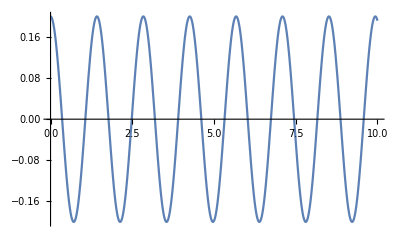

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```